# Задание № 9.

## Методы Монте-Карло

## Куценко Богдан Дмитриевич 20361

## Задание

Все задачи в этом задании взяты из методического пособия Войтишек А.В. Символьные и численные расчеты в физических приложениях. Вам нужно выполнить (воспроизвести) математические выкладки с помощью системы Wolfram Mathematica, реализовать генераторы, построить гистограммы и плотности распределения.

### Метод обратной функции распределения. Конструирование моделируемых плотностей

При численном решении задач теории переноса излучения широко используется индикатриса Хеньи-Гринстейна, представляющая собой плотность распределения косинуса угла рассеяния  u при столкновении “фотона” с частицей среды cледующего вида

f(u)=(1-μ^2)/(2(1+μ^2-2μ u)^(3/2)), u∈(-1,+1)

Плотность распределения зависит от параметра  μ∈(-1,1). Постройте метод генерации u в соответствии с эти распределением, постройте гистограммы + графики  плотностей распределения при разных μ (графики могут быть интерактивными).

```mathematica
Clear[HenieDistribution,initHenie,callHenie]
f[μ_]:=(1-μ^2)/(2(1+μ^2-2μ u))^(3/2)

Normalization =Assuming[-1<μ<1,Integrate[f[μ],{u,-1,1}]];

HenieDistribution[μ_]:=ProbabilityDistribution[f[μ]/Normalization,{u,-1,1}];


initHenie[prg_Symbol,μValue_]:=(
μ[prg]^=μValue;
s[prg] ^=NSolve[Rationalize[(CDF[HenieDistribution[μValue]]@u )]==Rationalize[r],u,Reals][[1]]
);

callHenie[prg_Symbol]:=
Module[{prgit=prg},
u/.s[prgit]/. r->RandomReal[]
]
```

```mathematica
Clear[genHenie]
initHenie[genHenie,3/10]
callHenie[genHenie]
```

{u→ConditionalExpression[(-245.+763. r+327. r^2)/(245.+420. r+180. r^2), 0<r<1.]}

0.877955

```mathematica
Clear[dataHenie,datagen]
initHenie[genHenie,3/10];

datagen[μ0_]:=Module[{μ=μ0},
initHenie[genHenie,μ];
Table[callHenie[genHenie],{10000}]
]



Manipulate[Show[Histogram[datagen[μ],Automatic,"PDF"],Plot[(PDF[HenieDistribution[μ]]@u ),{u,-1.,1.},PlotStyle->Directive[Red,Thick],PlotRange->Full],PlotLabel->StringTemplate["μ = `1` "][μ]],{{μ,3/10},-0.99,0.99}]
```

### Конструирование двумерного моделируемого вектора с зависимыми координатами

Сформулируйте стандартный метод моделирования случайного вектора и продемонстрируйте его на примере двумерного вектора (ξ, η), имеющего плотность распределения. Постройте 2-мерные гистограмму + плотность распределения.

f(u,v)=3 u^2(u+1)v^u e^(-u^3),  0<u<∞, 0<v<1

```mathematica
Clear[f,Distributionξ,callξ,callη,genξ,genη,initξ,initη,ξ0,η0,ξ]
f[u_,v_]:=3*u^2(u+1)v^(u)Exp[-u^3];
PDFξ=Assuming[0<u<∞ &&0<v<1,Integrate[f[u,v],{v,0,1}]]
Distributionξ:=ProbabilityDistribution[PDFξ,{u,-1,1}];


initξ[prg_Symbol]:=(
ξ[prg] ^=(-Log[r])^(1/3);
)

callξ[prg_Symbol]:=
Module[{prgit=prg},
ξ[prgit]/. r->RandomReal[]
]


initη[prg_Symbol]:=(
η[prg] ^=r^(1/(ξ+1));
);

callη[prg_Symbol,ξtemp_]:=
Module[{prgit=prg,ξ0=ξtemp},
η[prgit]/. r->RandomReal[]/.ξ->ξ0
]
Clear[genξ,genη]
initξ[genξ]
initη[genη]

vectorgen[prg1_Symbol,prg2_Symbol]:=Module[{prgξ=prg1,prgη=prg2},
ξ0=callξ[prgξ];
η0=callη[prgη,ξ0];
{ξ0,η0}
]


vectorgen[genξ,genη]
```

3 ⅇ^(-u^3) u^2

{0.422789,0.633905}

```mathematica
initξ[genξ]
initη[genη]

datavector=Table[vectorgen[genξ,genη],{10000}];
Show[Histogram3D[datavector,Automatic,"PDF"],Plot3D[f[u,v],{u,0.,2.},{v,0.,1.}]]
```

-Graphics3D-

### Метод дискретной суперпозиции

Требуется построить алгоритм моделирования случайной величины ξ, имеющей плотность распределения.

f(u)=(5u)/((1+u^2)^2)+(√2 π)/(8 u^2)sin(π/(2u)), 1<u<2

```mathematica
Clear[Superp1Distribution,Superp2Distribution,f,initSuperp,callSuperp]
f[u_]:= 5u/(1+u^2)^2+Sqrt[2]Pi/(8u^2)*Sin[Pi/(2u)]
p1=Integrate[5u/(1+u^2)^2,{u,1,2}]
p2=Integrate[Sqrt[2]Pi/(8u^2)*Sin[Pi/(2u)],{u,1,2}]
SuperpDistribution1:=ProbabilityDistribution[5u/(1+u^2)^2/p1,{u,1,2}];
SuperpDistribution2:=ProbabilityDistribution[Sqrt[2]Pi/(8u^2)*Sin[Pi/(2u)]/p2,{u,1,2}];
initSuperp[prg_Symbol]:=(
s1[prg] ^=NSolve[Rationalize[(CDF[SuperpDistribution1]@u )]==Rationalize[r],u,Reals][[1]];
s2[prg] ^=NSolve[Rationalize[(CDF[SuperpDistribution2]@u )]==Rationalize[r],u,Reals][[1]];
);

callSuperp[prg_Symbol]:=
Module[{prgit=prg},
α1=RandomReal[];
If[α1<3/4,u/.s1[prgit]/. r->RandomReal[],u/.s2[prgit]/. r->RandomReal[]]
]

initSuperp[genSuperp]
callSuperp[genSuperp]
```

3/4

1/4

1.32792

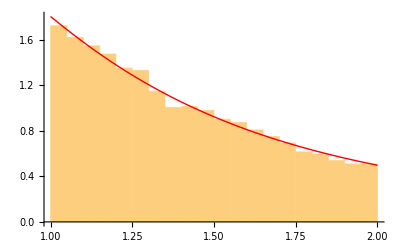

```mathematica
initSuperp[genSuperp]
dataSuperp=Table[callSuperp[genSuperp],{10000}];
Show[Histogram[dataSuperp,Automatic,"PDF"],Plot[f[u],{u,1.,2.},PlotStyle->Directive[Red,Thick]]]
```

### Метод исключения

Рассмотрим случайную величину ξ, имеющую плотность распределения (здесь lg - десятичный логарифм)

f(u)=1/(Ḡ(u^2 lg(u+10)+10)), 0 < u <1

Нормировка плотности распределения в элементарных функциях не вычисляется

Ḡ=(∫_0)^1 ⅆu/(u^2 lg(u+10)+10)

Реализуйте алгоритм метода исключения для этой случайной величины.

Как только у вас будет генератор вы можете оценить интеграл Ḡ методом Монте-Карло (как?). Оцените погрешность оценки Ḡ методом Монте-Карло. Как ведет себя погрешность с увеличением n числа разыгранных случайных величин (попробуйте n = 10, 100, 1000, 10000).

Сравните со значением Ḡ, которое дает NIntegrate.

Постройте гистограмму и плотность распределения.

```mathematica
Clear[G,f,fmajor,Normalization,callException,initException]

f[u_]:=1/(u^2Log[u+10]+10)
fmajor[u_]:=1/(u^2+10)

Normalization =Integrate[fmajor[u],{u,0,1}];
ExceptionDistribution:=ProbabilityDistribution[fmajor[u]/Normalization,{u,0,1}];


initMajor[prg_Symbol]:=(
s[prg] ^=NSolve[Rationalize[(CDF[ExceptionDistribution]@u )]==Rationalize[r],u,Reals][[1]];
);

callMajor[prg_Symbol]:=
Module[{prgit=prg},
u/.s[prgit]/. r->RandomReal[]
]
initMajor[genMajor]
callMajor[genMajor]

callException[prg_Symbol]:=Module[{prgit=prg},
ξ0=callMajor[prgit];
η0=RandomReal[]/(ξ0^2+10);
While[η0>f[ξ0],
ξ0=callMajor[prgit];
η0=RandomReal[]/(ξ0^2+10);];
ξ0
]

callException[genMajor]
```

0.0834125

0.262151

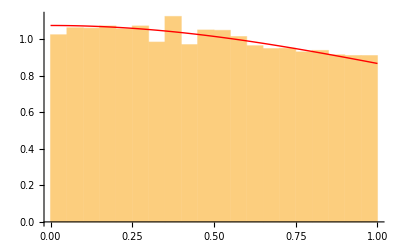

```mathematica
initMajor[genMajor]
dataException=Table[callException[genMajor],{10000}];
G=NIntegrate[1/(u^2Log[u+10]+10),{u,0,1}];
Show[Histogram[dataException,Automatic,"PDF"],Plot[f[u]/G,{u,0.,1.},PlotStyle->Directive[Red,Thick]]]
```

```mathematica
(*Оценка интеграла*)
Clear[n]
initMajor[genMajor];

intmonte[n_]:=Total[Table[f[callException[genMajor]],{n}]/n];
intmonteError[n0_]:=Module[{n=n0},
ξlsit=Table[f[callException[genMajor]],{n}];
Sqrt[(Total[ξlsit^2]-Total[ξlsit]^2/n)/(n-1)]
]

intmonte[1000]
NIntegrate[1/(u^2Log[u+10]+10),{u,0,1}]
```

0.0935192

0.0930556

```mathematica
intmonteError[10]
intmonteError[100]
intmonteError[1000]
intmonteError[10000]
intmonteError[100000]
```

0.00689749

0.00621585

0.00575153

0.00585228

0.00578453

### Выборка по важности

Реализуйте алгоритм выборки по важности для вычисления 4-кратного интеграла. Оцените дисперсию вычислений (точек потребуется достаточно много). Попробуйте сравнить с NIntegrate  (с разными стратегиями интегрирования и опциями вычислений)

I=1/(2π)^2(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)ⅇ^(-(x_1^2+x_2^2+x_3^2+x_4^2)/2)√(1+(sin^3(x_1 x_2 x_3 x_4))/12)ⅆ x_1ⅆ x_2ⅆ x_3ⅆ x_4

```mathematica
Clear[f,intmonte]


f[ξ1_,ξ2_,ξ3_,ξ4_ ]:=Sqrt[1+(Sin[ξ1*ξ2*ξ3*ξ4])^3/12];

ξ :=InverseCDF[NormalDistribution[0,1],RandomReal[]];
intmonte[n0_]:=Module[{n=n0},
ξlsit=Table[f[ξ,ξ,ξ,ξ],{n}];
Total[ξlsit^2]/(n)
]

intmonteDisp[n0_]:=Module[{n=n0},
ξlsit=Table[f[ξ,ξ,ξ,ξ],{n}];
(Total[ξlsit^2]-Total[ξlsit]^2/n)/(n-1)
]
```

```mathematica
intmonte[10000]

NIntegrate[1/(2Pi)^2Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1*x2*x3*x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞}]

NIntegrate[1/(2Pi)^2Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1*x2*x3*x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞},Method->"GlobalAdaptive"]

NIntegrate[1/(2Pi)^2Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1*x2*x3*x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞},Method->"MonteCarlo",MaxPoints->10000]
NIntegrate[1/(2Pi)^2Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1*x2*x3*x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞},Method->"AdaptiveQuasiMonteCarlo"]
```

1.00015

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999948 and 0.000180389 for the integral and error estimates.

0.999948

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999948 and 0.000180389 for the integral and error estimates.

0.999948

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 1.1191 and 0.0656296 for the integral and error estimates.

1.1191

0.977603

```mathematica
(*Оценка дисперсии*)
intmonteDisp[1000000]
```

0.00011632